# Analysis of the yeast datasets from http://deleteome.holstegelab.nl/

## Analysis of all mutants:

Import the yeast dataset of all mutants:

```mathematica
d=Import[".../deleteome_all_mutants_controls.txt","Table"];
```

Extract the wild-type and mutant data:

```mathematica
(wt=(2^(#[[2]]-#[[1]]/2)&/@Partition[#,3])&/@d[[3;;,4;;]]);
(mt=(2^(#[[2]]+#[[1]]/2)&/@Partition[#,3])&/@d[[3;;,4;;]]);
```

Extract the gene names for each of the datasets:

```mathematica
genenames=d[[3;;,3]];
```

Preprocessing the data as processed by Sun and Zhang: remove three outline strains, consider genes with mean expression larger than 7.72 10^-4 and compute the Z-score of each gene:

```mathematica
{ZNwt,ZNmt}=({#[[;;,1]]ᵀ,#[[;;,2]]}&@({(#[[1]]-Mean@#[[1]])/(StandardDeviation@#[[1]]),#[[2]]}&/@Select[{(#/(Total@#)&/@Delete[#ᵀ,{{1485},{1486},{1487}}])ᵀ,genenames}ᵀ,Mean@#[[1]]>7.72 10^-4&]))&/@{wt,mt};
```

Compute the principal components of the mutants and the wild-type replicates:

```mathematica
pcawt=PrincipalComponents[ZNwt[[1]]];
pcamt=PrincipalComponents[ZNmt[[1]]];
```

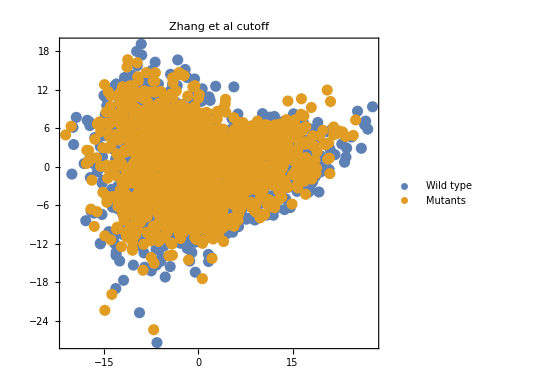

```mathematica
ListPlot[#[[;;,;;2]]&/@{pcawt,pcamt},AspectRatio->Automatic,PlotRange->All,PlotStyle->PointSize[.02],PlotLegends->{"Wild type","Mutants"},PlotLabel->"Zhang et al cutoff",Axes->False,Frame->True]
```

Consider also a log-transform instead of a Z-score normalization:

```mathematica
{ZNwtLog,ZNmtLog}=({#[[;;,1]]ᵀ,#[[;;,2]]}&@({Log10[#[[1]]+1],#[[2]]}&/@Select[{(#/(Total@#)&/@Delete[#ᵀ,{{1485},{1486},{1487}}])ᵀ,genenames}ᵀ,Mean@#[[1]]>7.72 10^-4&]))&/@{wt,mt};
```

```mathematica
pcawtLog=PrincipalComponents[ZNwtLog[[1]]];
pcamtLog=PrincipalComponents[ZNmtLog[[1]]];
```

Figure 2e:

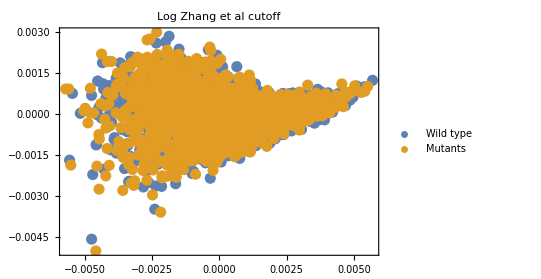

```mathematica
ListPlot[#[[;;,;;2]]&/@{pcawtLog,pcamtLog},AspectRatio->Automatic,PlotRange->All,PlotStyle->PointSize[.02],PlotLegends->{"Wild type","Mutants"},PlotLabel->"Log Zhang et al cutoff",Axes->False,Frame->True]
```

## Analysis of only the responsive mutants dataset:

Import the yeast dataset of only the responsive mutants:

```mathematica
d1=Import[".../deleteome_responsive_mutants_controls.txt","Table"];
```

```mathematica
(wt1=(2^(#[[2]]-#[[1]]/2)&/@Partition[#,3])&/@d1[[3;;,4;;]]);
(mt1=(2^(#[[2]]+#[[1]]/2)&/@Partition[#,3])&/@d1[[3;;,4;;]]);
```

```mathematica
genenames1=d1[[3;;,3]];
```

Preprocessing the responsive mutants data: consider genes with mean expression larger than 2 10^-4 (the exact threshold for the all mutant dataset leaves no genes), and compute the Z-score of each gene:

```mathematica
{ZNwt1,ZNmt1}=({#[[;;,1]]ᵀ,#[[;;,2]]}&@({(#[[1]]-Mean@#[[1]])/(StandardDeviation@#[[1]]),#[[2]]}&/@Select[{(#/(Total@#)&/@(#ᵀ))ᵀ,genenames1}ᵀ,Mean@#[[1]]>2 10^-4&]))&/@{wt1,mt1};
```

```mathematica
pcawt1=PrincipalComponents[ZNwt1[[1]]];
pcamt1=PrincipalComponents[ZNmt1[[1]]];
```

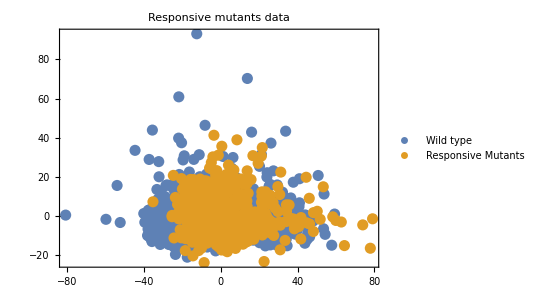

```mathematica
ListPlot[#[[;;,;;2]]&/@{pcawt1,pcamt1},AspectRatio->Automatic,PlotRange->All,PlotStyle->PointSize[.02],PlotLegends->{"Wild type","Responsive Mutants"},Axes->False,Frame->True,PlotLabel->"Responsive mutants data"]
```

Preprocessing the responsive mutants data: consider genes with mean expression larger than 2 10^-4 (the exact threshold for the all mutant dataset leaves no genes), and log transform the data:

```mathematica
{ZNwt1Log,ZNmt1Log}=({#[[;;,1]]ᵀ,#[[;;,2]]}&@({Log10[#[[1]]+1],#[[2]]}&/@Select[{(#/(Total@#)&/@(#ᵀ))ᵀ,genenames1}ᵀ,Mean@#[[1]]>2 10^-4&]))&/@{wt1,mt1};
```

```mathematica
pcawt1Log=PrincipalComponents[ZNwt1Log[[1]]];
pcamt1Log=PrincipalComponents[ZNmt1Log[[1]]];
```

Figure 2f:

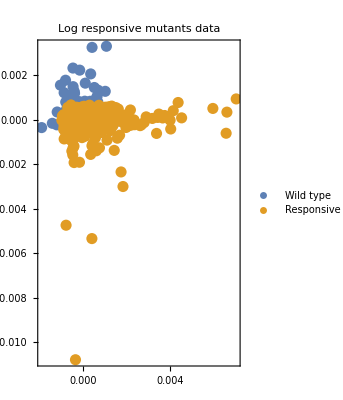

```mathematica
ListPlot[#[[;;,;;2]]&/@{pcawt1Log,pcamt1Log},AspectRatio->Automatic,PlotRange->All,PlotStyle->PointSize[.02],PlotLegends->{"Wild type","Responsive Mutants"},Axes->False,Frame->True,PlotLabel->"Log responsive mutants data"]
```